Разные графики до достижения 2 космической

Ускорение по осям

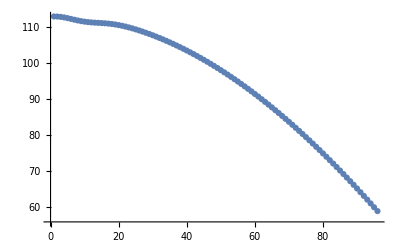

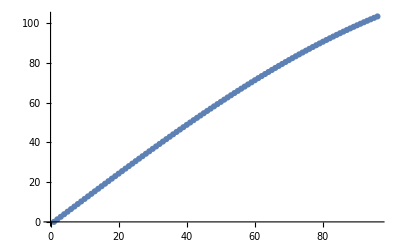

Масса и плотность воздуха

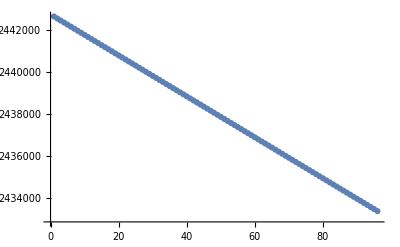

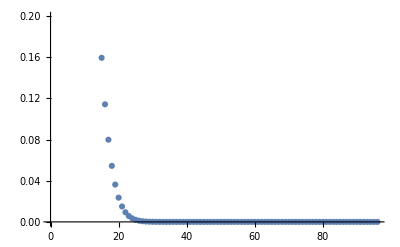

Смещение по осям

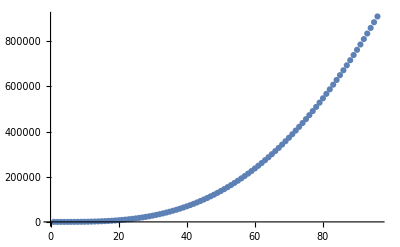

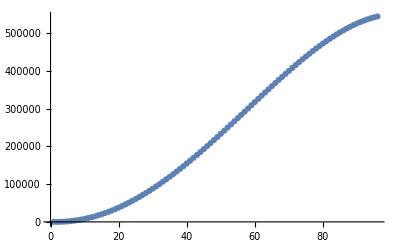

Скорость, полученная после выхода

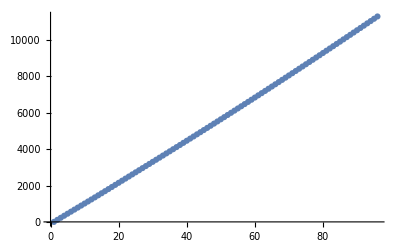

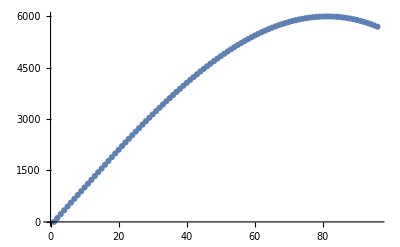

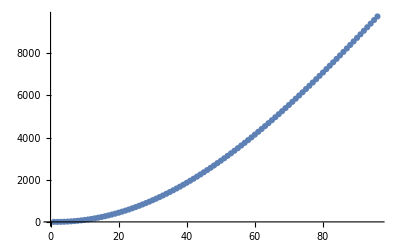

11291.6

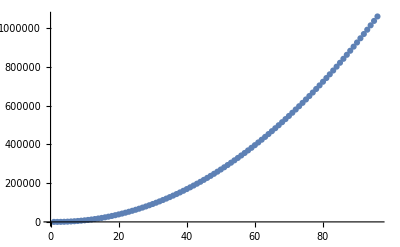

График суммарного ускорения

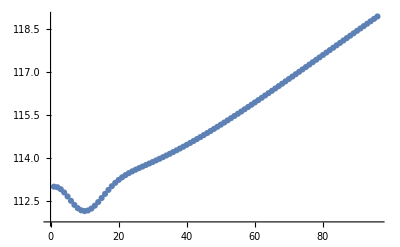

Среднее время перелета до Марса в днях

230.628

Cкорость у орбиты,время торможения и новая масса

{3515.09,63}

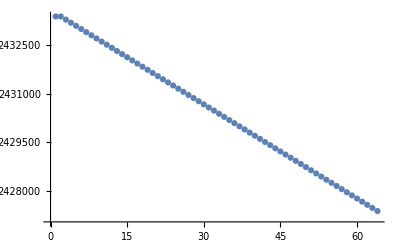

Время 1 оборота по оптимальной орбите Марса

6.06902

```mathematica
m0=2442619;
mp={};
mpnow=m0;
Gconts=6.67*(10^(-11));
Merth=5.978*(10^24);
Rerth=6371000;
R=8.31;
T=293;
Ftyga=300000000;
Spoper=16.2;
Cfr=0.5;
poo=1.204;
MAIR=29*10^(-3);
vtoplive=97.115;
t=0;
hn=0;
vyn=0;
vxn=0;
axn=0;
ayn=0;
Ftag={};
h={};
l={};
ln=0;
Vx={};
Vy={};
ax={};
ay={};
po={};
pi=3.14;
pon=0;
corner=0;
g=0;
Ftagn=0;
Ftygan=0;
vsecond=2*Gconts*Merth/(Rerth);
While[vxn^2+vyn^2<vsecond,corner=If[t<140,(t/300)*pi,(14/30)*pi];
mp=Append[mp,m0-vtoplive*t];
mpnow=Last[mp];
Ftag=Append[Ftag,Gconts*mpnow*Merth/((Rerth+hn)^2)];
Ftagn=Last[Ftag];
g=Ftagn/mpnow;
po=Append[po,poo*Exp[-MAIR*g*hn/(R*T)]];
pon=Last[po];
h=Append[h,vyn*t];
hn=Last[h];
l=Append[l,vxn*t];
ln=Last[l];
Vx=Append[Vx,axn*t];
vxn=Last[Vx];
Vy=Append[Vy,ayn*t];
vyn=Last[Vy];
ax=Append[ax,(Ftyga*Sin[corner]-Cfr*(pon*vxn*Spoper)/2)/mpnow];
axn=Last[ax];
ayn=((Ftyga*Cos[corner])-(Cfr*pon*vyn*vyn*Spoper/2)-Ftagn(*-(mpnow*vxn*vxn/(Rerth+hn))*))/mpnow;
ay=Append[ay,ayn];
t=t+1;]
Print["Разные графики до достижения 2 космической"];
Print["Ускорение по осям"]
ListPlot[ay]
ListPlot[ax]
Print["Масса и плотность воздуха"]
ListPlot[mp]
ListPlot[po]

Print["Смещение по осям"]
ListPlot[l]
ListPlot[h]


vyzemli=Sqrt[Last[Vy]^2+Last[Vx]^2];
Print["Скорость, полученная после выхода"];
ListPlot[Sqrt[Vy^2+Vx^2]]
ListPlot[Vy]
ListPlot[Vx]
Print[Sqrt[Last[Vy]^2+Last[Vx]^2]];
traectoria=Sqrt[h^2+l^2];
ListPlot[traectoria]
Print["График суммарного ускорения"];
a=Sqrt[ax^2+ay^2];
ListPlot[a]

distance=225000000000;
Print["Среднее время перелета до Марса в днях"];
Print[(distance/vyzemli)/(3600*24)]
t=0;
mpspace={mpnow};
Mmars=6.42*(10^23);
Rmars=3397000;
Vfrstdmars=Sqrt[Gconts*Mmars/(Rmars)];

While[vyzemli>=Vfrstdmars,aout=Ftyga/Last[mpspace];
mpspace=Append[mpspace,mpnow-vtoplive*t];
vyzemli-=Ftyga/Last[mpspace];
t+=1;]
Print["Cкорость у орбиты,время торможения и новая масса"];
Print[{vyzemli,t}];
ListPlot[mpspace]
Rorbiter=3.6*Rmars;
Lengthoforbiter=pi*2*Rorbiter;
Print["Время 1 оборота по оптимальной орбите Марса"]
Print[(Lengthoforbiter/vyzemli)/(3600)];
Terth=365;
Tmars=687;
Tdelta=((Terth*Tmars)/(Tmars-Terth));
```